Week-5

```mathematica
g[x_] = x^2
```

x^2

```mathematica
g[5]
```

25

```mathematica
g[2t]
```

4 t^2

```mathematica
gg[x_] = x^3
```

x^3

```mathematica
g2[y_] = Integrate[x^2, {x, 0 , y}]
```

y^3/3

Setting semi-colon will not leads to the result.

Module Function

```mathematica
ff[x_]:=Module[{}, x^2]
```

```mathematica
ff[x_]:= Module[{}, x^2]
```

```mathematica
ff[10]
```

100

```mathematica
ff[21]
```

441

```mathematica
speed[dist_, time_]:= Module[{spd}, spd = dist/time; Return[spd];]
```

```mathematica
speed[5,7]//N
```

0.714286

```mathematica
speed[10,2]
```

5

```mathematica
speed[dist_, time_]:= Module[{spd}, spd = dist/time; Return[spd];]
```

```mathematica
speed[2,1]//N
```

2.

Euler Method

Writing Euler Method as a Custom Function.

Implementation of Euler Method

```mathematica
f[t_, x_] = -2*x
```

-2 x

```mathematica
f[1.02,0.96]
```

-1.92

```mathematica
xi = 1;
ti=0;
tf=10;
nMax=500;
h = (tf-ti)/nMax//N
```

0.02

```mathematica
For[datalist={{ti,xi}};, 
Length[datalist]<= nMax, 
AppendTo[datalist, prev + {h, h f@@prev}], 
prev = Last[datalist]]
```

```mathematica
datalist//Last
```

{10.,1.36652×10^-9}

```mathematica
h f@@{0.1,2}
```

-0.08

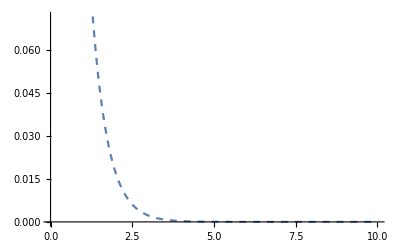

```mathematica
dataPlot=ListPlot[datalist, Joined->True, PlotStyle->Dashed ]
```

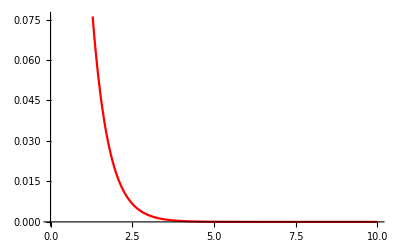

```mathematica
SolnPlot = Plot[E^(-2 t), {t,ti,tf}, PlotStyle->Red]
```

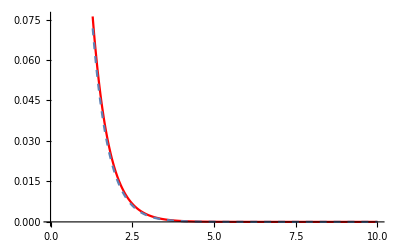

```mathematica
Show[SolnPlot, dataPlot]
```

```mathematica
datalist[[20, 1]]
```

0.38

```mathematica
{Exp[-2 datalist[[20,1]]], datalist[[20,2]]}
```

{0.467666,0.460419}

```mathematica
men = Table[Exp[-2 datalist[[20,1]]]-datalist[[20,2]], {n,1,Length[datalist]}]//Mean
```

0.00724723

```mathematica
h^2
```

0.0004

```mathematica
men - h^2
```

0.00684723

Euler’s Method as a function [Module Construct]

```mathematica
euler[ti_, tf_, xi_, func_, nMax_] := Module[{h, datalist, prev}, h = (tf - ti)/nMax//N;
For[datalist={{ti,xi}};, 
Length[datalist]<= nMax,
AppendTo[datalist, prev + {h, h f@@prev}], 
prev= Last[datalist]];

Return[datalist];
]
```

```mathematica
f1[t_,x_]=2 x
```

2 x

```mathematica
mydata = euler[0,10,1,f1, 1000];
```

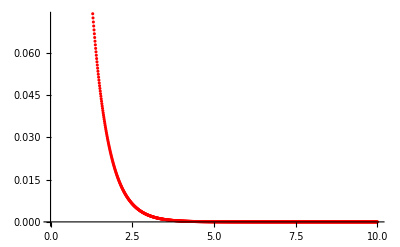

```mathematica
myPlot = ListPlot[euler[0,10,1,f1, 1000], PlotStyle->Red]
```

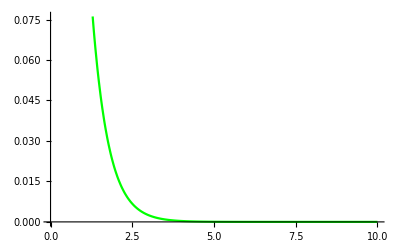

```mathematica
soluPlot = Plot[E^(-2 t), {t, 0,10}, PlotStyle-> Green, PlotStyle->Thick]
```

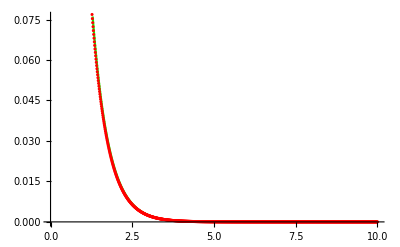

```mathematica
Show[soluPlot, myPlot]
```

```mathematica
error[data_, solfunc_] := Module[{tlist, xlist}, tlist = data[[;;, 1]];
xlist = data[[;;, 2]];
Return[tlist];
]
```

```mathematica
error[mydata, f1];
```

Now, More......

```mathematica
error[data_, solfunc_] := Module[{tlist, xlist, xtrue}, tlist = data[[;;, 1]];
xlist = data[[;;, 2]];
xtrue=solfunc/@tlist;
Return[xtrue];
]
```

```mathematica
soln[t_]= Exp[-2 t]
```

ⅇ^(-2 t)

```mathematica
error[mydata, soln];
```

Now, 
Further,

```mathematica
error[data_, solfunc_] := Module[{tlist, xlist, xtrue}, tlist = data[[;;, 1]];
xlist = data[[;;, 2]];
xtrue=solfunc/@tlist;
Return[xtrue - xlist//Abs//Mean ];
]
```

```mathematica
error[mydata, soln]
```

0.000501165

We can here, match the value of the error from tradition method, and here, using module construct. The answer for both the cases is same.
 
 All in One Go!
 Nicest!

0.000501165

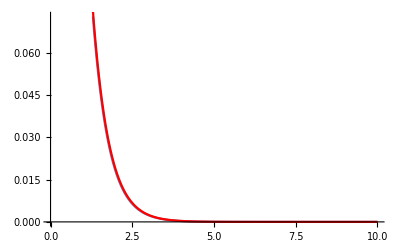

```mathematica
f1[t_,x_]=2 x;
soln[t_]= Exp[-2 t];
mydata = euler[0,10,1,f1,1000];
error[mydata, soln]
Show[ListPlot[mydata, Joined->True], Plot[soln[t], {t,0,10}, PlotStyle->Red]]
```

Changing the values of the function and solution function, will give the answer for different functions. Hence, generalizes this.

0.615401

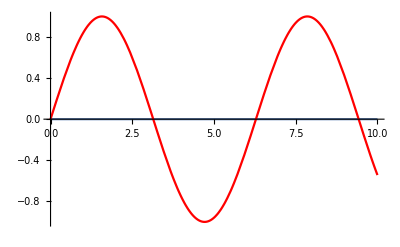

```mathematica
f1[t_,x_]= Cos[t];
soln[t_] = Sin[t];
mydata = euler[0,10,0,f1, 500];
error[mydata, soln]
Show[ListPlot[mydata, Joined->True], Plot[soln[t], {t,0,10}, PlotStyle->Red]]
```

```mathematica
error[mydata, soln]
```

0.615401

```mathematica
f1[t_,x_]= -2 x;
```

```mathematica
soln[t_]= E^(-2t);
```

```mathematica
Table[{(10/10^n)^2//N, error[euler[0,10,0,f1,500], soln]/((10/10^n)^n)},{n,1,5}]
```

{{1.,0.0509049},{0.01,5.09049},{0.0001,50904.9},{1.×10^-6,5.09049×10^10},{1.×10^-8,5.09049×10^18}}

Global Error in Euler’s Method and Application

```mathematica
Clear["Global`*"]
```

```mathematica
euler[ti_, tf_, xi_, func_, nMax_] := Module[{h, datalist, prev}, h = (tf - ti)/nMax//N;
For[datalist={{ti,xi}};, 
Length[datalist]<= nMax,
AppendTo[datalist, prev + {h, h f@@prev}], 
prev= Last[datalist]];

Return[datalist];
]
```

Mean Global Order is of the order of h, and that of the Local error is of the order of h^2.

```mathematica
error[dataset_, func_] := Module[{tlist, xlist, Fxlist}, tlist = dataset[[;;, 1]];
xlist = dataset[[;;, 2]];
Fxlist=func/@tlist;
Return[xlist-Fxlist//Abs//Mean];
]
```

```mathematica
f[t_, x_]= -x t
```

-t x

```mathematica
ff[t_]= ⅇ^(-t^2/2)
```

ⅇ^(-t^2/2)

```mathematica
Table[{(5.0/10^n), error[euler[0,5,1,f,10^n], ff]/(5.0/10^n)}, {n,1,4}]//N
```

{{0.5,0.0746396},{0.05,0.0639748},{0.005,0.0631697},{0.0005,0.0630899}}

The thing to notice here is, the number is becoming constant when divided by h, but when divided by h square, it will not be constant. This means, it is only proportional to h, and not to h^2. As h decreases, the value also decreases for the error.

Through Function

```mathematica
Through[{f,g,h}[x]]
```

{f[x],g[x],h[x]}

```mathematica
Through[{f,g,h}@@{t,x,y,z}]
```

{f[t,x,y,z],g[t,x,y,z],h[t,x,y,z]}

```mathematica
eulerGen[Func_, x0_, tf_, nMax_] := Module[{h, datalist, prev, next, rate}, 
h = (tf - x0[[1]])/nMax//N;
For[datalist={x0};, 
Length[datalist]<= nMax,
AppendTo[datalist,next], 
 prev = Last[datalist];
rate=Through[Func@@prev];
next = prev + h rate;
 ];
Return[datalist];
]
```

Problem of the LCR Circuit:-

```mathematica
dQ/dt= I;
dI/dt= -L/(R^2 C)Q - I;
X = (Q);
```

Now,

```mathematica
w = 200;
beta = √(w - 1/4);
(2.0 π)/beta
id[t_,charge_, current_] = 1;
chargeDot[t_, charge_, current_] = current;
currentDot[t_, charge_, current_] = -w charge - current;
initial = {0,1,0};
```

0.444566

```mathematica
data = eulerGen[{id, chargeDot, currentDot}, initial, 10, 10000];
```

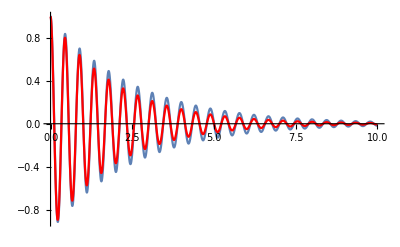

```mathematica
Show[ListPlot[data[[;;, 1;;2]], Joined-> True, PlotMarkers->None, PlotRange-> Full], Plot[ⅇ^(-t/2)Cos[beta t], {t,0,10}, PlotRange-> Full, PlotStyle->Red]]
```

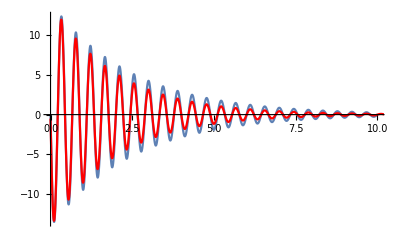

```mathematica
Show[ListPlot[data[[;;, {1,3}]], Joined-> True, PlotMarkers -> None, PlotRange->Full], Plot[-(ⅇ^(-t/2)/2)Cos[beta t]- ⅇ^(-t/2) beta Sin[t beta], {t,0,20}, PlotRange-> Full, PlotStyle->Red]]
```

Runge-Kutta Method for Solving ODE

RK2 Method or Euler Improved Method.

```mathematica
rk2[F_,X0_,tf_,nMax_]:=
Module[{h,datalist,prev,rate,rate1, next},
h=(tf-X0[[1]])/nMax//N;
For[datalist={X0},
 Length[datalist]<=nMax,
 AppendTo[datalist,next],
 prev=Last[datalist];
rate=F@prev;
rate1 = F@(prev+ h rate);
next=prev+h/2(rate+ rate1);
];
Return[datalist];
]
```

```mathematica
ratefunc[{t_,x_,v_}]={1,v,-v-4x-2 Sin[2t]+4 t^2+2 };
initial={0,1,0};
```

```mathematica
data2=rk2[ratefunc,initial,97,10000]
```

{{0,1,0},9999,{97.,9361.34,194.904}}
 |  |  |  |

RK4 Method

```mathematica
rk4[F_,Xθ_,tf_,nmax_]:=Module[{h,datalist,prev,rate1,rate2,rate3,rate4,next},h=(tf-Xθ[[1]])/nmax//N;
For[datalist={Xθ},Length[datalist]<=nmax,AppendTo[datalist,next],prev=Last[datalist];
rate1=F@prev;
rate2=F@(prev+h/2 rate1);
rate3=F@(prev+h/2 rate2);
rate4=F@(prev+h rate3);
next=prev+h/6(rate1+2 rate2+2 rate3+rate4);];
Return[datalist]]

ratefunc[{t_,x_,v_}]={1,v,Sin[t]+(t+2)Cos[t]-v-x};
initial={0,0,0};
```

{{0,0,0},{0.329867,0.106823,0.635991},{0.659734,0.404313,1.13424},{0.989602,0.827091,1.37925},{1.31947,1.27805,1.29693},{1.64934,1.64439,0.867769},{1.9792,1.81668,0.131973},{2.30907,1.70824,-0.814211},{2.63894,1.27179,-1.8307},{2.96881,0.510939,-2.75276},{3.29867,-0.515547,-3.41477},{3.62854,-1.69754,-3.67515},{3.95841,-2.88539,-3.43925},{4.28827,-3.90844,-2.6767},{4.61814,-4.59803,-1.43073},{4.94801,-4.81195,0.182299},{5.27788,-4.45714,1.9835},{5.60774,-3.50721,3.7513},{5.93761,-2.01231,5.24824},{6.26748,-0.0993372,6.25168},{6.59734,2.03806,6.58438},{6.92721,4.15898,6.14105},{7.25708,6.00238,4.90721},{7.58695,7.31871,2.96745},{7.91681,7.9023,0.501558},{8.24668,7.62039,-2.23174},{8.57655,6.43501,-4.92186},{8.90642,4.41442,-7.2416},{9.23628,1.73217,-8.8864},{9.56615,-1.3468,-9.61304},{9.89602,-4.49216,-9.273},{10.2259,-7.34359,-7.83604},{10.5558,-9.55193,-5.40064},{10.8856,-10.8213,-2.1895},{11.2155,-10.9473,1.47019},{11.5454,-9.84632,5.17994},{11.8752,-7.57192,8.51339},{12.2051,-4.31637,11.0651},{12.535,-0.39546,12.4992},{12.8648,3.78173,12.5923},{13.1947,7.75544,11.2647},{13.5246,11.0658,8.59685},{13.8544,13.3059,4.82711},{14.1843,14.1709,0.33162},{14.5142,13.4978,-4.41314},{14.844,11.2906,-8.88076},{15.1739,7.72711,-12.5533},{15.5038,3.14648,-14.9811},{15.8336,-1.98273,-15.8368},{16.1635,-7.1102,-14.958},{16.4934,-11.6629,-12.3724},{16.8232,-15.1092,-8.30146},{17.1531,-17.0204,-3.14347},{17.483,-17.123,2.56554},{17.8128,-15.336,8.2072},{18.1427,-11.7865,13.1479},{18.4726,-6.8036,16.8096},{18.8024,-0.888334,18.7375},{19.1323,5.33622,18.6551},{19.4622,11.1906,16.5014},{19.792,16.0133,12.4455},{20.1219,19.2349,6.8747},{20.4518,20.4452,0.358316},{20.7816,19.4443,-6.41034},{21.1115,16.2712,-12.6877},{21.4414,11.2074,-17.7617},{21.7712,4.75285,-21.0321},{22.1011,-2.42279,-22.0813},{22.431,-9.54963,-20.726},{22.7608,-15.8402,-17.0449},{23.0907,-20.5762,-11.3771},{23.4206,-23.1905,-4.29204},{23.7504,-23.3344,3.46741},{24.0803,-20.9221,11.0629},{24.4102,-16.1479,17.6512},{24.74,-9.47225,22.4775},{25.0699,-1.5777,24.9619},{25.3998,6.70029,24.7681},{25.7296,14.462,21.8472},{26.0595,20.841,16.4504},{26.3894,25.1011,9.10881},{26.7192,26.7207,0.581757},{27.0491,25.4557,-8.22174},{27.379,21.3734,-16.3398},{27.7088,14.8528,-22.8628},{28.0387,6.55023,-27.035},{28.3686,-2.66651,-28.342},{28.6984,-11.8085,-26.5727},{29.0283,-19.872,-21.8503},{29.3582,-25.9486,-14.6254},{29.6881,-29.3272,-5.63452},{30.0179,-29.5769,4.17499},{30.3478,-26.6006,13.7449},{30.6777,-20.6531,22.02},{31.0075,-12.3205,28.0645},{31.3374,-2.46322,31.1678},{31.6673,7.87274,30.927},{31.9971,17.5668,27.2983},{32.327,25.5453,20.6087},{32.6569,30.9003,11.528},{32.9867,32.9926,1.00196}}

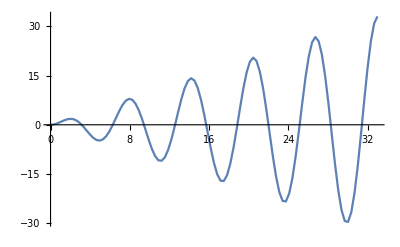

```mathematica
data4=rk4[ratefunc,initial,21 Pi/2,100]
ListPlot[data4[[;;,1;;2]],Joined->True,PlotMarkers->None,PlotRange->Full]
```

```mathematica
Clear["Global`*"]
```

```mathematica
DSolve[{x'[t] ==(-7x[t] +9660)  x[t], x[0] ==690}, x[t], t]
```

{{x[t]→(1380 ⅇ^(9660 t))/(1+ⅇ^(9660 t))}}

```mathematica
Limit[(1380 ⅇ^(9660/ t))/(1+ⅇ^(9660 /t)),t->0]
```

Indeterminate